```mathematica
ClearAll["Global`*"]
```

```mathematica
str:=2
K[n_] := If[ n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
K2[n_] := If[Floor[n^(1/str)]==n^(1/str),K[n^(1/str)],0]
K7[n_] := K2[n]-If[ Floor[Log[2,n]]==Log[2,n],n^(1/str) /Log[2,n],0]
P[n_,0]=1; 
P[n_, k_] := P[n,k] = Sum[ K7[j]P[Floor[n/j],k-1],{j,2,n}]
En[n_] := En[n] = Sum[ 1/(k!) P[n,k],{k,0, Log[2,n]}]
En[n_,z_] := En[n,z] = Sum[ (z^k)/(k!) P[n,k],{k,0, Log[2,n]}]
en[n_] := Sum[ 1/(k!) p[n,k],{k,0, Log[2,n]}]
LAdd[n_] := Sum[ (2^(1/str))^k/k,{k,1,Log[2,n]}]
PP[n_,k_] := PP[n,k]=Sum[ 1/k-PP[Floor[n/j],k+1],{j,2,n}]
PR[n_]:=Sum[ FullSimplify[MangoldtLambda[j]/Log[j]],{j,2,n}]
```

```mathematica
P[10^str,1]+LAdd[10^str]
```

16/3

```mathematica
PR[10]
```

16/3

```mathematica
N[LAdd[10^str]-LAdd[2^str]+LogIntegral[2]]
```

5.45268

```mathematica
N[LogIntegral[10]]
```

6.1656

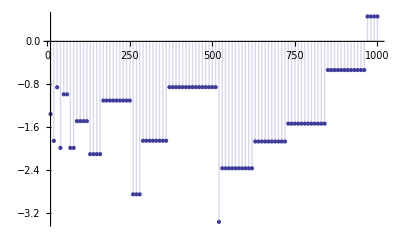

```mathematica
DiscretePlot[{P[n,1]},{n,10,1000,10}]
```

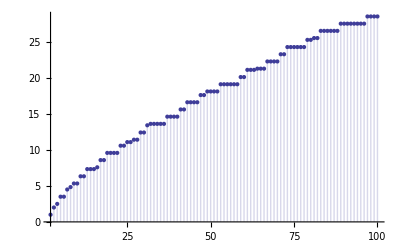

```mathematica
DiscretePlot[{P[n^str,1]+LAdd[n^str]},{n,2,100}]
```

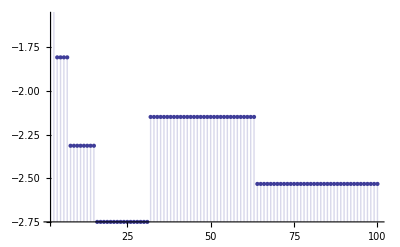

```mathematica
DiscretePlot[{P[n,1]},{n,2,100}]
```

```mathematica
Table[{n,FullSimplify[en[n]]},{n,2,50}]//TableForm
```

2 | -√2
3 | 0
4 | 1
5 | 0
6 | 0
7 | 0
8 | -√2
9 | 1
10 | 0
11 | 0
12 | 0
13 | 0
14 | 0
15 | 0
16 | 1
17 | 0
18 | -√2
19 | 0
20 | 0
21 | 0
22 | 0
23 | 0
24 | 0
25 | 1
26 | 0
27 | 0
28 | 0
29 | 0
30 | 0
31 | 0
32 | -√2
33 | 0
34 | 0
35 | 0
36 | 1
37 | 0
38 | 0
39 | 0
40 | 0
41 | 0
42 | 0
43 | 0
44 | 0
45 | 0
46 | 0
47 | 0
48 | 0
49 | 1
50 | -√2

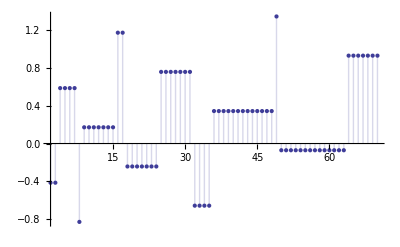

```mathematica
DiscretePlot[En[n],{n,2,70}]
```

```mathematica
Table[ {n, En[n]},{n,1,100}]//TableForm
```

```mathematica
Table[ {n, FullSimplify[P[n,2]-P[n-1,2]]},{n,1,100}]//TableForm
```

1 | 0
2 | 0
3 | 0
4 | 2
5 | 0
6 | 0
7 | 0
8 | 0
9 | 0
10 | 0
11 | 0
12 | 0
13 | 0
14 | 0
15 | 0
16 | 8/3
17 | 0
18 | -2 √2
19 | 0
20 | 0
21 | 0
22 | 0
23 | 0
24 | 0
25 | 0
26 | 0
27 | 0
28 | 0
29 | 0
30 | 0
31 | 0
32 | √2
33 | 0
34 | 0
35 | 0
36 | 0
37 | 0
38 | 0
39 | 0
40 | 0
41 | 0
42 | 0
43 | 0
44 | 0
45 | 0
46 | 0
47 | 0
48 | 0
49 | 0
50 | -2 √2
51 | 0
52 | 0
53 | 0
54 | 0
55 | 0
56 | 0
57 | 0
58 | 0
59 | 0
60 | 0
61 | 0
62 | 0
63 | 0
64 | 184/45
65 | 0
66 | 0
67 | 0
68 | 0
69 | 0
70 | 0
71 | 0
72 | -(4 √2)/3
73 | 0
74 | 0
75 | 0
76 | 0
77 | 0
78 | 0
79 | 0
80 | 0
81 | 1
82 | 0
83 | 0
84 | 0
85 | 0
86 | 0
87 | 0
88 | 0
89 | 0
90 | 0
91 | 0
92 | 0
93 | 0
94 | 0
95 | 0
96 | 0
97 | 0
98 | -2 √2
99 | 0
100 | 0

```mathematica
FullSimplify[Expand[en[256]]]
```

0

```mathematica
LAddx[n_,st_] := Sum[ st^k/k,{k,1,Log[st,n]}]
```

```mathematica
Table[{N[2^(1/n)],N[LAddx[100,2^(1/n)]-LAddx[2,2^(1/n)]+LogIntegral[2]]},{n,1,60}]//TableForm
```

2. | 26.7785
1.41421 | 31.1928
1.25992 | 27.6806
1.18921 | 29.5759
1.1487 | 30.7722
1.12246 | 29.0556
1.10409 | 29.9624
1.09051 | 30.6612
1.08006 | 29.523
1.07177 | 30.1159
1.06504 | 30.6101
1.05946 | 29.7585
1.05477 | 30.1983
1.05076 | 30.5807
1.04729 | 29.9003
1.04427 | 30.2497
1.04162 | 29.6746
1.03926 | 29.995
1.03716 | 30.2848
1.03526 | 29.7931
1.03356 | 30.0628
1.03201 | 30.3103
1.0306 | 29.8808
1.0293 | 30.1137
1.02811 | 30.3297
1.02702 | 29.9485
1.026 | 30.1534
1.02506 | 30.345
1.02419 | 30.0023
1.02337 | 30.1851
1.02261 | 29.8714
1.0219 | 30.046
1.02123 | 30.2111
1.0206 | 29.9239
1.02 | 30.0823
1.01944 | 30.2327
1.01891 | 29.9679
1.01841 | 30.1129
1.01793 | 30.2511
1.01748 | 30.0055
1.01705 | 30.139
1.01664 | 30.2668
1.01625 | 30.0378
1.01588 | 30.1616
1.01552 | 29.9458
1.01518 | 30.0659
1.01486 | 30.1813
1.01455 | 29.9784
1.01425 | 30.0906
1.01396 | 30.1987
1.01368 | 30.0072
1.01342 | 30.1124
1.01316 | 30.214
1.01292 | 30.0329
1.01268 | 30.1319
1.01245 | 30.2278
1.01223 | 30.0558
1.01202 | 30.1494
1.01182 | 29.985
1.01162 | 30.0765

```mathematica
N[LogIntegral[100]]
```

30.1261

```mathematica
LAddx[n_,st_] := Sum[ st^k/k,{k,1,Log[st,n]}]
```

```mathematica
LAddx[100,1.000001]-LAddx[2,1.000001]+LogIntegral[2]
```

30.1262-2.46016×10^-10 ⅈ

```mathematica
LAddx[100,1.001]-LAddx[2,1.001]+LogIntegral[2]
```

30.1267